## mathematical tips

## absolute values

One of the advantages of use Mathematica is its support to mathematical notation instead of use just codes. In many occasions it's easiest to focus on the maths and ignore the code generation like in

```mathematica
∫_0^∞ f[x]ⅆx
```

However, some notations are not present by standard like the absolute value for instance. We need to write

```mathematica
Abs[1+ⅈ]^2
```

Not that it's a big issue but it would be better write something like

```mathematica
(|1+ⅈ|)^2
```

Luckily Mathematica has a representation for bracketing using vertical bars called BracketingBar.

```mathematica
BracketingBar[x,y]
```

|x,y|

And we can associate this operation by assuming that, every time we use a single input, we are talking about absolute value.

```mathematica
BracketingBar[x_] := Abs[x]
```

```mathematica
(|1+ⅈ|)^2
```

2

To type the vertical brackets use Escl|Esc for the left bar and Escr|Esc for the right bar.

## tensor product

Instead of write

```mathematica
KroneckerProduct[a, b]
```

we could do just

```mathematica
a⊗b
```

This can be done associating the CircleTimes with the KroneckerProduct.

```mathematica
CircleTimes = KroneckerProduct;
```

```mathematica
With[{a=({{Subscript[a, 1,1], Subscript[a, 2,1]}, {Subscript[a, 1,2], Subscript[a, 2,2]}}),b=({{Subscript[b, 1,1], Subscript[b, 2,1]}, {Subscript[b, 1,2], Subscript[b, 2,2]}})},
a⊗b
]
```

(a_(1,1) b_(1,1) | a_(1,1) b_(2,1) | a_(2,1) b_(1,1) | a_(2,1) b_(2,1)
a_(1,1) b_(1,2) | a_(1,1) b_(2,2) | a_(2,1) b_(1,2) | a_(2,1) b_(2,2)
a_(1,2) b_(1,1) | a_(1,2) b_(2,1) | a_(2,2) b_(1,1) | a_(2,2) b_(2,1)
a_(1,2) b_(1,2) | a_(1,2) b_(2,2) | a_(2,2) b_(1,2) | a_(2,2) b_(2,2))

It also works for multiple inputs like

```mathematica
With[{a=({{Subscript[a, 1,1], Subscript[a, 2,1]}, {Subscript[a, 1,2], Subscript[a, 2,2]}}),b=({{Subscript[b, 1,1], Subscript[b, 2,1]}, {Subscript[b, 1,2], Subscript[b, 2,2]}}),c=({{Subscript[c, 1,1], Subscript[c, 2,1]}, {Subscript[c, 1,2], Subscript[c, 2,2]}})},
a⊗b⊗c
]
```

(a_(1,1) b_(1,1) c_(1,1) | a_(1,1) b_(1,1) c_(2,1) | a_(1,1) b_(2,1) c_(1,1) | a_(1,1) b_(2,1) c_(2,1) | a_(2,1) b_(1,1) c_(1,1) | a_(2,1) b_(1,1) c_(2,1) | a_(2,1) b_(2,1) c_(1,1) | a_(2,1) b_(2,1) c_(2,1)
a_(1,1) b_(1,1) c_(1,2) | a_(1,1) b_(1,1) c_(2,2) | a_(1,1) b_(2,1) c_(1,2) | a_(1,1) b_(2,1) c_(2,2) | a_(2,1) b_(1,1) c_(1,2) | a_(2,1) b_(1,1) c_(2,2) | a_(2,1) b_(2,1) c_(1,2) | a_(2,1) b_(2,1) c_(2,2)
a_(1,1) b_(1,2) c_(1,1) | a_(1,1) b_(1,2) c_(2,1) | a_(1,1) b_(2,2) c_(1,1) | a_(1,1) b_(2,2) c_(2,1) | a_(2,1) b_(1,2) c_(1,1) | a_(2,1) b_(1,2) c_(2,1) | a_(2,1) b_(2,2) c_(1,1) | a_(2,1) b_(2,2) c_(2,1)
a_(1,1) b_(1,2) c_(1,2) | a_(1,1) b_(1,2) c_(2,2) | a_(1,1) b_(2,2) c_(1,2) | a_(1,1) b_(2,2) c_(2,2) | a_(2,1) b_(1,2) c_(1,2) | a_(2,1) b_(1,2) c_(2,2) | a_(2,1) b_(2,2) c_(1,2) | a_(2,1) b_(2,2) c_(2,2)
a_(1,2) b_(1,1) c_(1,1) | a_(1,2) b_(1,1) c_(2,1) | a_(1,2) b_(2,1) c_(1,1) | a_(1,2) b_(2,1) c_(2,1) | a_(2,2) b_(1,1) c_(1,1) | a_(2,2) b_(1,1) c_(2,1) | a_(2,2) b_(2,1) c_(1,1) | a_(2,2) b_(2,1) c_(2,1)
a_(1,2) b_(1,1) c_(1,2) | a_(1,2) b_(1,1) c_(2,2) | a_(1,2) b_(2,1) c_(1,2) | a_(1,2) b_(2,1) c_(2,2) | a_(2,2) b_(1,1) c_(1,2) | a_(2,2) b_(1,1) c_(2,2) | a_(2,2) b_(2,1) c_(1,2) | a_(2,2) b_(2,1) c_(2,2)
a_(1,2) b_(1,2) c_(1,1) | a_(1,2) b_(1,2) c_(2,1) | a_(1,2) b_(2,2) c_(1,1) | a_(1,2) b_(2,2) c_(2,1) | a_(2,2) b_(1,2) c_(1,1) | a_(2,2) b_(1,2) c_(2,1) | a_(2,2) b_(2,2) c_(1,1) | a_(2,2) b_(2,2) c_(2,1)
a_(1,2) b_(1,2) c_(1,2) | a_(1,2) b_(1,2) c_(2,2) | a_(1,2) b_(2,2) c_(1,2) | a_(1,2) b_(2,2) c_(2,2) | a_(2,2) b_(1,2) c_(1,2) | a_(2,2) b_(1,2) c_(2,2) | a_(2,2) b_(2,2) c_(1,2) | a_(2,2) b_(2,2) c_(2,2))

To type ⊗ use Escc*Esc.

## inner product

For physicists is quite convenient write inner products using the traditional ⟨·,·⟩ instead of dot product as Mathematica uses as standard. That can be done defining

```mathematica
AngleBracket[x_?VectorQ,y_?VectorQ] := x*.y
AngleBracket[x_?MatrixQ,y_?MatrixQ] := (x†.y)⟦1,1⟧
```

This double definition is necessary because Mathematica sees

```mathematica
{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],…}
```

as "vector" while

```mathematica
({{Subscript[x, 1]}, {Subscript[x, 2]}, {Subscript[x, 3]}, {⋮}})
```

as a matrix N×1 and since we expect the result of the inner product be a number we need to consider both cases

```mathematica
With[{u={Subscript[u, 1],Subscript[u, 2]},v={Subscript[v, 1],Subscript[v, 2]}},
⟨u,v⟩
]
```

v_1 Conjugate[(u_1)]+v_2 Conjugate[(u_2)]

```mathematica
With[{u=({{Subscript[u, 1]}, {Subscript[u, 2]}}),v=({{Subscript[v, 1]}, {Subscript[v, 2]}})},
⟨u,v⟩
]
```

v_1 Conjugate[(u_1)]+v_2 Conjugate[(u_2)]

An advantage of use the inner product this way is to get probabilities in quantum mechanics like in

```mathematica
With[{U=({{Subscript[U, 1,1], Subscript[U, 1,2]}, {Subscript[U, 2,1], Subscript[U, 2,2]}}),v=({{0}, {1}}),w=({{1}, {0}})},
(|⟨v,U.w⟩|)^2 
]
```

Abs[U_(2,1)]^2

## subscript as index

Okay, this one is just fancy. We can use subscript as index for vectors and matrices. For that we just need to define

```mathematica
Subscript[x_?ListQ, y__] := Part[x,y]
```

```mathematica
With[{x=Range[3]},
∑_(i=1)^3 (|Subscript[x, i]|)^2
]
```

(|1|)^2+(|2|)^2+(|3|)^2

```mathematica
With[{x=Array[#1+#2&,{2,2}]},
∑_(i=1)^2 ∑_(j=1)^2 (|Subscript[x, i,j]|)^2
]
```

(|2|)^2+2 (|3|)^2+(|4|)^2

Thanks to the constraint ?ListQ it cannot affects symbols that are not list, vector or matrices.

```mathematica
{Subscript[λ, 1],Subscript[θ, 2,3],Subscript[2, 1]}
```

{λ_1,θ_(2,3),2_1}

## vectorization

A nice trick to solve differential equations with matrices like

ⅆρ/ⅆt=L ρ L+L ρ+ρ L

is use vectorization which means, essentially, convert a matrix into a vector.

From a physicist point of view, vectorize a density matrix means take a density matrix

ρ=∑_n λ_n|λ_n⟩⟨λ_n|

and write it as a vector

ρ⃗=∑_n λ_n|λ_n⟩⊗|λ_n⟩*

Notice that the second ket keep the conjugate, it was just transposed.

As effect, such transformation results in

A ρ B≡A⊗Transpose[B] ρ⃗

Thus the differential equation becomes

(ⅆ ρ⃗)/ⅆt=(L⊗Lᵀ+L ⊗𝟙+𝟙⊗Lᵀ)ρ⃗=ℒ ρ⃗ ⟶ ρ⃗(t) = ⅇ^ℒ ρ⃗

We define the vectorization with

```mathematica
OverVector[m_?MatrixQ] := {Flatten[m]}ᵀ
```

If we just apply the Flatten function, it will transform the matrix into a list.

```mathematica
With[{ρ=({{Subscript[ρ, 1,1], Subscript[ρ, 1,2]}, {Subscript[ρ, 2,1], Subscript[ρ, 2,2]}})},
Flatten[ρ]
]
```

{ρ_(1,1),ρ_(1,2),ρ_(2,1),ρ_(2,2)}

By wrapping the Flatten with curly brackets we create a 1×N matrix.

```mathematica
With[{ρ=({{Subscript[ρ, 1,1], Subscript[ρ, 1,2]}, {Subscript[ρ, 2,1], Subscript[ρ, 2,2]}})},
{Flatten[ρ]}
]
```

(ρ_(1,1) | ρ_(1,2) | ρ_(2,1) | ρ_(2,2))

Since we want an N×1 matrix we need to transpose the last result

```mathematica
With[{ρ=({{Subscript[ρ, 1,1], Subscript[ρ, 1,2]}, {Subscript[ρ, 2,1], Subscript[ρ, 2,2]}})},
{Flatten[ρ]}ᵀ
]
```

(ρ_(1,1)
ρ_(1,2)
ρ_(2,1)
ρ_(2,2))

To type the vector notation type first Ctrl7 and then EscvecEsc.

```mathematica
With[{ρ=({{Subscript[ρ, 1,1], Subscript[ρ, 1,2]}, {Subscript[ρ, 2,1], Subscript[ρ, 2,2]}})},
ρ⃗
]
```

(ρ_(1,1)
ρ_(1,2)
ρ_(2,1)
ρ_(2,2))

Now we need a easy way to return the vector back into a matrix form. We do that by define

```mathematica
vec2mat[v_?VectorQ] := With[{l=Length[v]},
	ArrayReshape[v, {√l,√l}]
]

vec2mat[v_?MatrixQ] := Block[{lin,col},
	{lin,col} = Dimensions[v];
	ArrayReshape[v, {√lin,√lin}] /; col==1
]
```

We need two definitions because, if we ask for instance, the eigenstates of ⅇ^ℒ in the example above it will return a "vector" (a list). But if we want to create a sort of inverse function of our definition for the vectorization we need to handle a matrix N×1.

```mathematica
With[{ρ=({{Subscript[ρ, 1,1], Subscript[ρ, 1,2]}, {Subscript[ρ, 2,1], Subscript[ρ, 2,2]}})},
vec2mat[ρ⃗]==ρ
]
```

True

```mathematica
vec2mat[{a,b,c,d}]==vec2mat[({{a}, {b}, {c}, {d}})]
```

True

The conditional /; on the matrix version helps to guarantee that only N×1 matrices will be accepted.

```mathematica
vec2mat[({{a, b}, {c, d}})]
```

vec2mat((a | b
c | d))

## fancy set notation

This one is completely useless, it's just to look nice when we use Simplify or any other function that has the same kind of constraints.

```mathematica
ℤ = Integers;
ℚ = Rationals;
ℝ = Reals;
ℂ = Complexes;
```

Then we are able to write

```mathematica
Simplify[g[n,x],{x∈ℝ,n∈ℤ}]
```

## fancy identity notation

```mathematica
Subscript[𝟙,n_] := IdentityMatrix[n];
```

```mathematica
{Subscript[𝟙, 2],Subscript[𝟙, 3],Subscript[𝟙, 4]}
```

{(1 | 0
0 | 1),(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

## logical operators

For functions defined with Piecewise clauses it's convenient to define an operator

```mathematica
Otherwise = True;
```

to express the general case like,

```mathematica
f[x_]:=Piecewise[{{x^2, x>0}, {0, Otherwise}}]
```

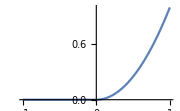

```mathematica
Plot[f[x],{x,-1,1}]
```